# Quick Computations

```mathematica
?Graph
```

Graph[{e_1,e_2,…}] yields a graph with edges e_j.
Graph[{v_1,v_2,…},{e_1,e_2,…}] yields the graph with vertices v_i and edges e_j. 
Graph[{…,w_i[v_i,…],…},{…,w_j[e_j,…],…}] yields a graph with vertex and edge properties defined by the symbolic wrappers w_k.

```mathematica
?GraphPlot
```

GraphPlot[g] generates a plot of the graph g.
GraphPlot[{v_i1→v_j1,v_i2→v_j2,…}] generates a plot of the graph in which vertex v_ik is connected to vertex v_jk.
GraphPlot[{{v_i1→v_j1,lbl_1},…}] associates labels lbl_k with edges in the graph.
GraphPlot[m] generates a plot of the graph represented by the adjacency matrix m.

{{0,0,0,0},{1,0,0,0},{1,1,0,0},{1,1,0,0}}

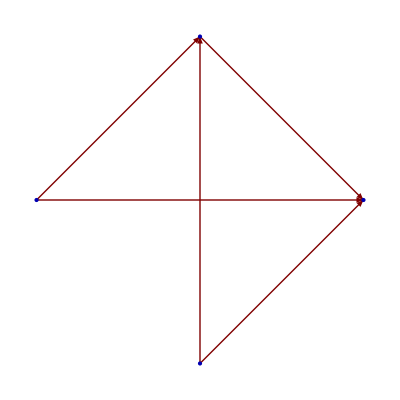

```mathematica
Module[{adj,i,j,selfweight,graphs},
j=0;
adj = {{0,0,0},{1,0,0},{1,1,0}};
graphs=[];
While[j<1,
j+=1;
AppendTo[graphs,adj];
i = RandomInteger[{1,Length[adj]}];
selfweight = adj[[i]][[i]];
AppendTo[adj,adj[[i]]];
adj = Transpose[adj];
AppendTo[adj,adj[[i]]];
adj = Transpose[adj];
];
Print[adj];
GraphPlot[adj,DirectedEdges->True,MultiedgeStyle->True,Method->"CircularEmbedding"]
]
```

```mathematica
?Animate
```

Animate[expr,{u,u_min,u_max}] generates an animation of expr in which u varies continuously from u_min to u_max. 
Animate[expr,{u,u_min,u_max,du}] takes u to vary in steps du. 
Animate[expr,{u,{u_1,u_2,…}}] makes u take on discrete values u_1, u_2, …. 
Animate[expr,{u,…},{v,…},…] varies all the variables u, v, ….

```mathematica
{1,2}
```

Thread::tdlen: Objects of unequal length in {1,2}+{3} cannot be combined.

{3}+{1,2}

```mathematica
?Append
```

Append[expr,elem] gives expr with elem appended. 
Append[elem] represents an operator form of Append that can be applied to an expression.